## Tents, Humps, and Wiggles

Split an interval 0≤x≤L up with m equally spaced internal points
	x_i=i h
where h=L/(m+1) and build a variety of piecewise polynomial nodal functions.

```mathematica
p[h_]:= a0 + a1 h + a2 h^2
p'[0]
```

a1

### Tents

Piecewise linear functions are represented by tent functions.

One way to think abut computing the formula is by matching the 4 coefficients in a piecewise linear function
	L(x)=Piecewise[{{-h<x<0, a0+a1 x}, {0<x<h, b0+b1 x}}]
and match the conditions L continuous at -h, h, and 0 and L[0]=1.  These 4 conditions in the four unknowns completely determine the Tent function. Should I do a reference element and scale and shift?

```mathematica
{a0+a1 x, b0 + b1 x}/.Solve[{a0==1,b0==1,a0 - a1 h ==0, b0+b1 h ==0  }]
```

{{1+x/h,1-x/h}}

```mathematica
Lin[x_]:= Piecewise[{
{1.0 +x,-1<x<0},
{1.0-x,0<x<1}
},0]
(*Tent[i_,h_][x_]:= Piecewise[{
{1.0 +(x- i h)/h,(i-1)h<x<i h},
{1.0-(x-i h)/h,i h<x<(i+1)h}
},0]*)
Tent[i_,h_][x_]:=Lin[(x-i h)/h]
{L,m}={π,5}; h=L/(m+1.0);
f[x_]:=Sin[x]
us=Table[ f[i h],{i,1,m}]; u[x_]=Sum[us⟦i⟧Tent[i,h][x],{i,1,m}];
TabView[{
"Tents"->Plot[{Tent[1,h][x],Tent[2,h][x]},{x,0,L},
PlotRange->All],
"Interpolation"->Plot[{f[x],u[x]},{x,0,L}]}]
```

12

### Humps and Wiggles

One way to think abut computing the formula is by again matching coefficients in a piecewise polynomial function to satisfy
	L is continuous at -h, h, and 0.
	L' is continuous at -h, h, and 0
and either 
matching the 6 coefficients in a piecewise quadratic function
	Q(x)=Piecewise[{{-h<x<0, a0+a1 x+a2 x^2}, {0<x<h, b0+b1 x+ b2 x^2}}]
and match the conditions L and L' continuous at -h, h, and 0 and L[0]=1.  These 4 conditions in the four unknowns completely determine the Tent function. Should I do a reference element and scale and shift?

```mathematica
Qa[x_]:=a0+a1 x + a2 x^2+a3 x^3; Qb[x_]:=b0+b1 x + b2 x^2+b3 x^3
Eqv={
Qa[0]==Qb[0]==1,
Qa'[0]==Qb'[0]==0,
Qa[-h]==0, Qa'[-h]==0,
Qb[h]==0, Qb'[h]==0};
{Qa[x],Qb[x]}/.Solve[Eqs,{a0,a1,a2,a3,b0,b1,b2,b3}]
Eqs={
Qa[0]==Qb[0]==0,
Qa'[0]==Qb'[0]==1,
Qa[-h]==0, Qa'[-h]==0,
Qb[h]==0, Qb'[h]==0};
{Qa[x],Qb[x]}/.Solve[Eqs,{a0,a1,a2,a3,b0,b1,b2,b3}]
```

{{1-(3 x^2)/h^2-(2 x^3)/h^3,1-(3 x^2)/h^2+(2 x^3)/h^3}}

{{x+(2 x^2)/h+x^3/h^2,x-(2 x^2)/h+x^3/h^2}}

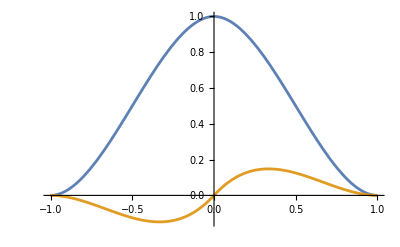

```mathematica
Qv[x_]:= Piecewise[{
{1-3 x^2-2 x^3, -1<x≤0},
{1-3 x^2+2 x^3, 0<x<1}
},0]
Qs[x_]:= Piecewise[{
{x+2 x^2+x^3, -1<x≤0},
{x-2 x^2+x^3, 0<x<1}
},0]
Plot[{Qv[x],Qs[x]},{x,-1,1}]
```

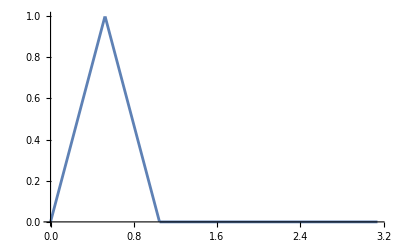

```mathematica
ITent[i_,h_][x_]:= Piecewise[{
{a0+1.0 x +(x- i h)^2/(2h),(i-1)h<x<i h},
{a0+1.0x-(x-i h)^2/(2h),i h<x<(i+1)h}
},0]

{L,m}={π,5}; h=L/(m+1.0);
Plot[ ITent[0,1,h]'[x],{x,0,L}]
```

Integrating a gives a wiggle functions

Piecewise quartic/quintic functions can represent localized hump and wiggle functions.

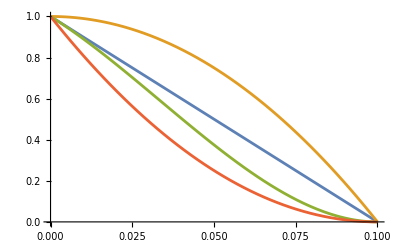

```mathematica
h=0.1;
Plot[ {1- x/h,(1-(x/h)^2),(1-(x/h)^2)(1-x/h),(1-x/h)^2},{x,0,h}]
```

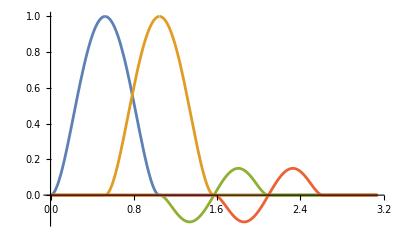

```mathematica
Hump[i_,h_][x_]:= Piecewise[{
{(x/h-(i-1) )^2(x/h-(i+1) )^2,(i-1)h<x<(i+1) h}
},0]
Wiggle[i_,h_][x_]:= Piecewise[{
{(x/h-(i-1) )^2(x-i h)(x/h-(i+1) )^2,(i-1)h<x<(i+1) h}
},0]
{L,m}={π,5}; h=L/(m+1.0);
f[x_]:=Sin[x]
us=Table[ f[i h],{i,1,m}]; dus=Table[ f'[i h],{i,1,m}]; 
u[x_]=Sum[us⟦i⟧Hump[i,h][x]+dus⟦i⟧ Wiggle[i,h][x],{i,1,m}];
Plot[{Hump[1,h][x],Hump[2,h][x],Wiggle[3,h][x],Wiggle[4,h][x]},{x,0,L},PlotRange->All]
```

```mathematica
{L,m}={π,64}; h=L/(m+1.0);
f[x_]:=x Cos[x](x-L)
us=Table[ f[i h],{i,1,m}]; 
dus=Table[ f'[i h],{i,1,m}]; 
u[x_]=Sum[us⟦i⟧Hump[i,h][x]+dus⟦i⟧ Wiggle[i,h][x],{i,1,m}];
TabView[{
"Humps&Wiggles"->Plot[{Hump[1,h][x],Hump[2,h][x],Wiggle[1,h][x],Wiggle[2,h][x]},{x,0,L},
PlotRange->All],
"Interpolation"->Plot[{f[x],u[x]},{x,0,L}]},2]
```

12

```mathematica
Table[u[i h],{i,1,m}]-us
Table[u'[i h],{i,1,m}]-dus
```

{2.77556×10^-17,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{8.88178×10^-16,-4.44089×10^-16,6.66134×10^-15,-1.33227×10^-14,Indeterminate,2.08722×10^-14,-3.64153×10^-14,-9.99201×10^-15,-9.99201×10^-15,Indeterminate,-5.01821×10^-14,-1.02141×10^-14,-9.99201×10^-15,Indeterminate,Indeterminate,1.29924×10^-13,-8.60423×10^-15,1.30562×10^-13,-2.36478×10^-13,Indeterminate,1.09246×10^-13,-2.03837×10^-13,Indeterminate,-1.37668×10^-14,-1.56097×10^-13,2.22045×10^-14,-1.1724×10^-13,Indeterminate,-7.50511×10^-14,Indeterminate,-1.90958×10^-14,-7.54952×10^-15,Indeterminate,3.81917×10^-14,Indeterminate,-1.82077×10^-14,1.03917×10^-13,Indeterminate,1.43441×10^-13,Indeterminate,1.78746×10^-13,-2.12275×10^-13,3.93241×10^-13,1.35447×10^-14,1.13243×10^-14,Indeterminate,4.75286×10^-13,-5.00988×10^-13,4.92495×10^-13,-1.13798×10^-15,-3.83027×10^-15,-6.43929×10^-15,Indeterminate,4.58966×10^-13,4.38538×10^-13,Indeterminate,3.85247×10^-13,-2.17604×10^-14,Indeterminate,Indeterminate,2.30482×10^-13,-3.01981×10^-14,Indeterminate,8.12683×10^-14}

## Guitar Strings

### FD Dirichlet-Dirichlet

#### Second order FD.

```mathematica
n=48;h=π/(n+1); 
A=1.0/h^2 SparseArray[{Band[{1,1}]->2,Band[{1,2}]->-1, Band[{2,1}]->-1},{n,n}];
λs=Reverse[Eigenvalues[A,-20]];
ListLogLogPlot[{λs, Table[i^2,{i,20}]},Joined->{False,True},
PlotLabel->λs⟦1;;5⟧]
```

#### 4th order FD.

```mathematica
Clear[f,x,dx]
ResourceFunction["FiniteDifferenceStencil"][f''[x],{f[x-2dx],f[x-dx],f[x],f[x+dx],f[x+2dx]},f,x]
n=48;h=π/(n+1); 
A=1.0/h^2 SparseArray[{
Band[{1,1}]->5/2,
Band[{1,2}]->-4/3, Band[{2,1}]->-4/3,
 Band[{1,3}]->1/12,Band[{3,1}]->1/12},{n,n}];
λs=Reverse[Eigenvalues[A,-20]];
ListLogLogPlot[{λs, Table[i^2,{i,20}]},Joined->{False,True},
PlotLabel->λs⟦1;;5⟧]
```

#### 6th order FD.

```mathematica
Clear[f,x,dx]
ResourceFunction["FiniteDifferenceStencil"][f''[x],{f[x-3dx],,f[x-2dx],f[x-dx],f[x],f[x+dx],f[x+2dx],f[x+3dx]},
f,x]
n=48;h=π/(n+1); 
A=1.0/h^2 SparseArray[{
Band[{1,1}]->49/18,
Band[{1,2}]->-3/2, Band[{2,1}]->-3/2,
 Band[{1,3}]->3/20,Band[{3,1}]->3/20,
 Band[{1,4}]->-1/90,Band[{4,1}]->-1/90
},{n,n}];
λs=Reverse[Eigenvalues[A,-20]];
ListLogLogPlot[{λs, Table[i^2,{i,20}]},Joined->{False,True},
PlotLabel->λs⟦1;;5⟧]
```

### FE Dirichlet-Dirichlet

The weak form is ∫_0^π u'(x)v'(x)dx

#### Fourier Basis

The Fourier basis sin(i x) satisfies D-D boundary conditions and gives a diagonal stiffness matrix.

```mathematica
n=6;
ϕ[i_][x_]:=√(2/π)Sin[i x]
Plot[{ϕ[1][x],ϕ[2][x],ϕ[3][x],ϕ[4][x]},{x,0, π}]
A=Table[ Integrate[ϕ[i]'[x]ϕ[j]'[x],{x,0, π}],
{i,n},{j,n}]
```

It is hard to compute the zero entries numerically.

```mathematica
n=6
AbsoluteTiming[
Quiet[
A=Table[ NIntegrate[ϕ[i]'[x]ϕ[j]'[x],{x,0, π}],
{i,n},{j,n}]
];
]
Eigenvalues[A]
```

#### Tent Basis

The Tent basis gives a tridiagonal stiffness matrix. The tents at the interior modes satisfy D-D conditions. It is a bit crazy to do the integration.  The superposition of these tent function linearly interpolates the weights at the nodes.

```mathematica
n=6;
ϕ[i_,n_][x_]:=Piecewise[{
{1+n(x/π-i/n),(i-1)/n<x/π< i/n },
{1-n(x/π-i/n), i/n<x/π< (i+1)/n }
},0]
Plot[{ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

The integrands for the stiffness functions are piecewise constant! Integrate and NIntegrate work fine.

```mathematica
n=12;
AbsoluteTiming[
A=Table[ NIntegrate[ϕ[i,n]'[x]ϕ[j,n]'[x],{x,0, π}],
{i,n},{j,n}];
]
MatrixPlot[A]
Eigenvalues[1.0*A]
```

#### Polynomial Basis: Mark 1

The polynomial basis 
	x (x/π-i/n)(x-π)
that got dreamed up should not work. They are all combinations of x,x^2,and x^3.

```mathematica
ϕ[i_,n_][x_]:=x(x-(i π)/n)(x-π)
n=5;
Plot[{ϕ[0,n][x],ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

The integrands for the stiffness functions are polynomials! Integrate works fine for small systems but will get slow for big systems. NIntegrate complains about some zero entries and will get slow for large systems.

```mathematica
n=12;
A=1.0*Table[ Integrate[ϕ[i,n]'[x]ϕ[j,n]'[x],{x,0, π}],
{i,0,n},{j,0,n}];
Eigenvalues[A]
```

#### Polynomial Basis: Mark 2

The polynomial basis 
	x (π_(j=1)^(n-1)(x/π-j/(n+1)))/(x/π-i/(n+1))(x-π)=
that got dreamed up should work. They are LI.

```mathematica
ϕ[i_,n_][x_]:=x Product[(x/π-j/(n+1)),{j,1,i-1}]Product[(x/π-j/(n+1)),{j,i+1,n}](x-π)
n=5;
Plot[{ϕ[0,n][x],ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

Thing is we might as well use the easier basis 
	x*x^i*(x-π)
for i=0,1,2,3,n-1.  The funny normalization makes ∫ϕ^2=1

```mathematica
Clear[i,n,x]
ϕ[i_][x_]:=√((30+47 i+24 i^2+4 i^3)/π^(5+2 i))x*x^i*(x-π)
Plot[{ϕ[0][x],ϕ[1][x],ϕ[2][x],ϕ[3][x],ϕ[4][x],ϕ[5][x]},{x, 0 ,π},PlotRange->All]
```

```mathematica
n=12;
A=1.0*Table[ Integrate[ϕ[i]'[x]ϕ[j]'[x],{x,0, π}],
{i,0,n},{j,0,n}];
Eigenvalues[A]
```

## Beam Strings

#### Fourier Bi-Bi Basis

```mathematica
ϕ[i_][x_]:=√(60/π^5)x Sin[i x](x-π)
Clear[i,j]
Integrate[ ϕ[i]''[x]ϕ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}
Integrate[ ϕ[i]''[x]ϕ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}
FullSimplify[Integrate[ ϕ[i][x]ϕ[i][x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
```

```mathematica
Plot[ Evaluate[Table[ϕ[i][x],{i,1, 7}]],{x,0,π},
PlotLegends->Automatic]
```

#### Fourier SS-SS Basis

```mathematica
ϕ[i_][x_]:=√(60/π^5)x Sin[i x](x-π)
ψ[i_][x_]:=√(60/π^5)x Cos[i x](x-π)
Clear[i,j]
FullSimplify[Integrate[ ϕ[i]''[x]ϕ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
Integrate[ ϕ[i]''[x]ϕ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}
FullSimplify[Integrate[ ϕ[i][x]ϕ[i][x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
FullSimplify[Integrate[ ψ[i]''[x]ψ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
Integrate[ ψ[i]''[x]ψ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}
FullSimplify[Integrate[ ψ[i][x]ψ[i][x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
```

```mathematica
FullSimplify[Integrate[ ψ[i]''[x]ϕ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
FullSimplify[Integrate[ ψ[i]''[x]ϕ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)} ]
```

```mathematica
n=3 10^3;
A=RandomReal[{-1,1},{n,n}];
AbsoluteTiming[λ=Eigenvalues[A];]
```

```mathematica
Plot[ Evaluate[Table[ϕ[i][x],{i,1, 7}]],{x,0,π},
PlotLegends->Automatic]
Plot[ Evaluate[Table[ψ[i][x],{i,0, 7}]],{x,0,π},
PlotLegends->Range[0,7]]
```

#### Fourier Bi-Bi Kalimba Basis

Think about this!

```mathematica
ϕ[i_][x_]:=x Sin[i x](x-a)(x-π)
Clear[i,j]
FullSimplify[Integrate[ ϕ[i]''[x]ϕ[j]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
FullSimplify[Integrate[ ϕ[i]''[x]ϕ[i]''[x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
FullSimplify[Integrate[ ϕ[i][x]ϕ[i][x],{x,0,π}]/.{Sin[k_ π]:>0,Cos[k_ π]:>(-1^k)}]
```

```mathematica
a=1.2;
Plot[ Evaluate[Table[ϕ[i][x],{i,1, 7}]],{x,0,π},
PlotLegends->Automatic]
```

#### Beam “Tent” aka piecewise “humps and wiggles” Basis

Explain why?

```mathematica
Clear[p1,p2]
p1[h_][x_]=x^2(a0 + a1 x)(x-2h)^2
p2[h_][x_]=x^2(b0 + b1 x)(x-2h)^2
Simplify[{p1[h][h]==1, p1[h]'[h]==0}]
Simplify[{p2[h][h]==0, p2[h]'[h]==1}]
```

So a1 = 0 and a0=1/h^4.
So b1 = 1/h^4 and b0=-1/h^3

```mathematica
p1[h_][x_]=Simplify[x^2(1/h^4 + 0 x)(x-2h)^2]
p2[h_][x_]=Simplify[x^2(-1/h^3+1/h^4 x)(x-2h)^2]
Plot[{p1[1][x],p2[1][x]},{x,0, 2}]
```

Could put more Degrees of Freedom (DOF) inside each interval using polynomials or sines.  More DOF would mean we could have bigger intervals that would mean more possible whammy bar movement.

```mathematica
(* Hump functions *)
(* NOTE: I ended up paramatarizing both sets of functions a lot more than you did just to make the process a little more clear to me - let me know if you'd like me to clean them up a bit more! *)
```

```mathematica
n=5;
L = Pi;
h = L/(n+1);
ϕ[i_,n_][x_]:=Piecewise[{
{(x-(i-1)*L/(n+1))^2((x-(i-1)*L/(n+1))-2h)^2/h^4,(i-1)h<x< (i+1)*h }
},0]
Plot[{ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

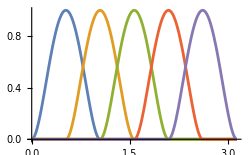
```mathematica
-Graphics-

(* Wiggle functions *)
ϕ[i_,n_][x_]:=Piecewise[{
{(x-(i-1)*L/(n+1))^2((x-(i-1)*L/(n+1))-2h)^2(-1/h^3+(x-(i-1)*L/(n+1))/h^4),(i-1)h<x< (i+1)*h }
},0]
Plot[{ϕ[1,n][x],ϕ[2,n][x],ϕ[3,n][x],ϕ[4,n][x],ϕ[5,n][x]},{x, 0 ,π},PlotRange->All]
```

Building Block matrices.

```mathematica
A11= RandomReal[{0,1},{3,4}];
A12= RandomReal[{-1,0},{3,6}];
A13= RandomReal[{2,6},{3,7}];
A21= RandomReal[{-1,1},{4,4}];
A22= RandomReal[{-1,1},{4,6}];
A= ArrayFlatten[ {
{A11, A12, A13},
{A21, A22, 0}
}];
MatrixPlot[A]
```

The integrands for the stiffness functions are ! Integrate and NIntegrate work fine.

```mathematica
n=12;
AbsoluteTiming[
A=Table[ NIntegrate[ϕ[i,n]'[x]ϕ[j,n]'[x],{x,0, π}],
{i,n},{j,n}];
]
MatrixPlot[A]
Eigenvalues[1.0*A]
```

## Possibilities

Possibilities

1) Explainer for Guitar Strings
Target Audience ODE Class Lin Alg background

2) Explainer for BI-BI Beam
Target Audience ODE Class Lin Alg background

3) Kalimba
Target Audience ODE Class Lin Alg background

4) Tuning shaped beams  “Marimba”
Target Audience ODE Class Lin Alg background

Questions:
Physics equations explained or not. 
Data?
Guitar FE and/or FD?
BI-BI beam FE and/or FD?
Kalimba and Marimba FE?

Audio output?
Animation output?
Delivery mechanism? 

∂_xx (a(x) ∂_xx u) =  ±  b(x) u_tt
u_xxxx=± u_tt

weak or variational form or virtual displacement 

∫∂_xx (a(x) ∂_xx u) v(x) dx  =  ±  ∫ b(x) v(x) u_tt dx
∫a(x) ∂_xx u v_xx(x) dx  + Boundary Terms =  ±  ∫ b(x) v(x) u_tt dx

∫ u_xx v_xx dx= κ∫v u_tt dx

```mathematica
{a1,a2,a3,a4,a5}={1.1,-2.1,0.3,0.4,0.4}
u[x_,t_]:= a1 Cos[ 1000 t] Sin[1 x]+ a2 Cos[ 2000 t] Sin[2 x]+ a3 Cos[ 3000 t] Sin[3 x]+ a4 Cos[ 4000 t] Sin[4 x]+ a5 Cos[12000 t] Sin[12 x]
Plot[u[x,0],{x,0, π}];
Manipulate[ Plot[u[x,t],{x,0, π},PlotRange->{-4,4}],{t,0, 12/1000,0.1/1000}]
Play[u[π/2,t],{t,0, 3}]
Play[u[1.0,t],{t,0, 3}]
```